### Draw regions illuminated by dipole’s magnetic region. Assume r1 = [0,0,0]; Todo: use lots of points, save in a cool file format, color negative in one color and positive in the other, show how overlap happens

```mathematica
3500 Hz, Mag 
gamma = 42480000 Hz/T  (42.48 MHz)
F = gamma*B

What is magnetic saturation?
```

```mathematica
N[3500/42480000]
Do contours of 3500 pm 2500/2
```

0.0000823917

```mathematica
μ0=4π 10^-7;
Msat=  1.36 10^6; (* steel in 3T*)
r1 = 0.0025; (*mm radius sphere*)
m1 = {0,0,4/3 π r1^3 Msat}; (*magnetization of first dipole*)
m2 =  {0,0,4/3 π r1^3 Msat};  (*magnetization of second dipole*)
rg =.06;
γ = 42480000;(* 42480000 Hz/T  (42.48 MHz/T)*)
Freq = 3500;
BW = 2500;
BField[r2_] := μ0/(4π)(3 r2/Norm[r2]((r2/Norm[r2]).m1)-m1)/Norm[r2]^3;
RegionPlot3D[r2 = {x,y,z};BField[r2]⟦3⟧>Freq/γ, { x,-rg,rg},{ y,-rg,rg},{ z,-rg,rg}]
```

-Graphics3D-

```mathematica
BB =Graphics3D[{Gray,Sphere[{0,0,0},r1]}]
```

-Graphics3D-

```mathematica
negPlot =RegionPlot3D[r2 = {x,y,z};BField[r2][[3]]>Freq/γ, { x,-rg,rg},{ y,-rg,rg},{ z,-rg,rg},PlotStyle->{Directive[Red,Opacity[0.5]]},Mesh->None, PlotPoints->50,AxesLabel->{"x [m]","y [m]","z [m]"},ViewPoint-> {0.9,-π,1.1},ViewVertical->{0.8,0.5,-0.09},TicksStyle->Directive[16],LabelStyle->Directive[18]];
Show[negPlot,BB]
```

-Graphics3D-

```mathematica
posPlot =RegionPlot3D[r2 = {x,y,z};BField[r2]⟦3⟧<-Freq/γ, { x,-rg,rg},{ y,-rg,rg},{ z,-rg,rg},PlotStyle->{Directive[Blue,Opacity[0.8]]},Mesh->None, PlotPoints->50,AxesLabel->{"x [m]","y [m]","z [m]"},
ViewPoint-> {0.9,-π,1.1},ViewVertical->{0.8,0.5,-0.09},TicksStyle->Directive[16],LabelStyle->Directive[18]];
Show[ posPlot,BB]
```

-Graphics3D-

```mathematica
Show[negPlot, posPlot,BB]
```

-Graphics3D-

```mathematica
-Graphics3D-//Options
```

{AutomaticImageSize→True,Axes→True,AxesLabel→{x,y,z},BoxRatios→{1,1,1},ImageSize→{355.865,342.521},PlotRange→{{-0.12,0.12},{-0.12,0.12},{-0.12,0.12}},PlotRangePadding→{Scaled[0.02],Scaled[0.02],Scaled[0.02]},ViewPoint→,ViewVertical→{0.844545,0.508386,-0.168188}}

### Draw 2D contours illuminated by dipole’s magnetic region. Assume r1 = [0,0,0]; Todo: use lots of points, save in a cool file format, color negative in one color and positive in the other, show how overlap happens

```mathematica
Clear[y]
√(x^2+y^2)
```

√(x^2+y^2)

```mathematica
N[2^(1/3)]
```

1.25992

```mathematica
r1 = 0.005; (*mm radius sphere*)
γ = 42480000;(* 42480000 Hz/T  (42.48 MHz/T)*)
Freq = {1500,2500};(*offset*)

dxy = r1((Msat  μ0 γ)/(3 Freq))^(1/3);
dz =r1 ((2Msat  μ0 γ)/(3 Freq))^(1/3);
StringForm["for r_s=``, d_xy=``, d_z=`` (all in m), Freq_offset = ``Hz",NumberForm[r1,4],NumberForm[dxy,4],NumberForm[dz,5],NumberForm[Freq,5]]
```

for r_s="0.005", d_xy={"0.1263", "0.1066"}, d_z={"0.15918", "0.13426"} (all in m), Freq_offset = {"1500", "2500"}Hz

for r_s="0.0025", d_xy="0.04763", d_z="0.060006" (all in m)

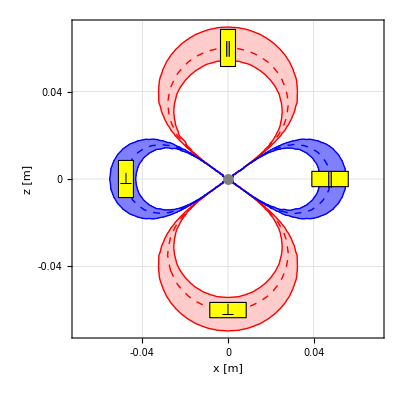

```mathematica
μ0=4π 10^-7;
Msat=  1.36 10^6; (* steel in 3T*)
r1 = 0.0025; (*mm radius sphere*)
m1 = {0,4/3 π r1^3 Msat}; (*magnetization of first dipole*)
m2 =  {0,4/3 π r1^3 Msat};  (*magnetization of second dipole*)
rg =.07;
(*dz = 0.125;
dxy = 0.098;*)

γ = 42480000;(* 42480000 Hz/T  (42.48 MHz/T)*)
Freq = 3500;(*offset*)
BW = 2500;
dxy = r1((Msat  μ0 γ)/(3 Freq))^(1/3);
dz =r1 ((2Msat  μ0 γ)/(3 Freq))^(1/3);
StringForm["for r_s=``, d_xy=``, d_z=`` (all in m)",NumberForm[r1,4],NumberForm[dxy,4],NumberForm[dz,5]]

mkRad = 0.0035; (*MR spot radius*)
mkHLength = 0.0085;(*MR-spot half-length*)
BField2D[{x_,y_}] := μ0/(4π)(3{x,y}/(√(x^2+y^2))(({x,y}/(√(x^2+y^2))).m1)-m1)/((√(x^2+y^2))^3);
ContourPlot[-(Msat r1^3 (x^2-2 z^2) μ0)/(3 (x^2+z^2)^(5/2)), { x,-rg,rg},{ z,-rg,rg},Contours->{(-(Freq-BW/2))/γ,(-(Freq))/γ,(-(Freq+BW/2))/γ,(Freq-BW/2)/γ,(Freq)/γ,(Freq+BW/2)/γ},ContourStyle->{Blue,Directive[Blue,Dashed],Blue,Red,Directive[Red,Dashed],Red},ContourShading->{None,Lighter[Blue,0.5],Lighter[Blue,0.5],None,Lighter[Red,0.8],Lighter[Red,0.8],None},Epilog->{Gray,Disk[{0,0},r1],
Yellow,EdgeForm[Black],
Rectangle[{-mkRad,dz-mkHLength},{mkRad,dz+mkHLength},RoundingRadius->0.005],
Rectangle[{-mkHLength,-(dz-mkRad)},{mkHLength,-(dz+mkRad)},RoundingRadius->0.005],
Rectangle[{dxy-mkHLength,-mkRad},{dxy+mkHLength,mkRad},RoundingRadius->0.005],
Rectangle[{-(dxy-mkRad),-mkHLength},{-(dxy+ mkRad),mkHLength},RoundingRadius->0.005],
Black,
Text[Style["⊥",16],{0,-dz}],
Text[Style["∥",16],{0,+dz}],
Text[Style["⊥",16],{-dxy,0}],
Text[Style["∥",16],{dxy,0}]
},FrameLabel-> {"x [m]","z [m]"},FrameTicks->{{-0.04,0,0.04},{-0.04,0,0.04},{},{}},PerformanceGoal->"Quality",FrameTicksStyle->Directive[16],LabelStyle->Directive[18],GridLines->Automatic,AspectRatio->1]
```

High Quality Publication version

```mathematica
rg =.075;
contourDensityPlot[-(Msat r1^3 (x^2-2 z^2) μ0)/(3 (x^2+z^2)^(5/2)), { x,-rg,rg},{ z,-rg,rg},
Contours->{(-(Freq-BW/2))/γ,(-(Freq))/γ,(-(Freq+BW/2))/γ,(Freq-BW/2)/γ,(Freq)/γ,(Freq+BW/2)/γ},Frame->True,

ContourStyle->{Blue,Directive[Blue,Dashed],Blue,Red,Directive[Red,Dashed],Red},
ContourShading->{None,Lighter[Blue,0.5],Lighter[Blue,0.5],None,Lighter[Red,0.8],Lighter[Red,0.8],None},
Epilog->{Gray,Disk[{0,0},r1],
Yellow,EdgeForm[Black],
Rectangle[{-mkRad,dz-mkHLength},{mkRad,dz+mkHLength},RoundingRadius->0.005],
Rectangle[{-mkHLength,-(dz-mkRad)},{mkHLength,-(dz+mkRad)},RoundingRadius->0.005],
Rectangle[{dxy-mkHLength,-mkRad},{dxy+mkHLength,mkRad},RoundingRadius->0.005],
Rectangle[{-(dxy-mkRad),-mkHLength},{-(dxy+ mkRad),mkHLength},RoundingRadius->0.005],
Black,
Text[Style["⊥",16],{0,-dz}],
Text[Style["∥",16],{0,+dz}],
Text[Style["⊥",16],{-dxy,0}],
Text[Style["∥",16],{dxy,0}]
},FrameLabel-> {"x [m]","z [m]"},FrameTicks->{{-0.04,0,0.04},{-0.04,0,0.04},{},{}},
PerformanceGoal->"Quality",FrameTicksStyle->Directive[16],LabelStyle->Directive[18],ImageSize-> Medium,"ShadingOpacity"->0.7,GridLines->Automatic,AspectRatio->Automatic,MaxRecursion->5]
```

-Graphics-

#### What is the revolution solid of the maximum magnetic field as it revolves around an axis?

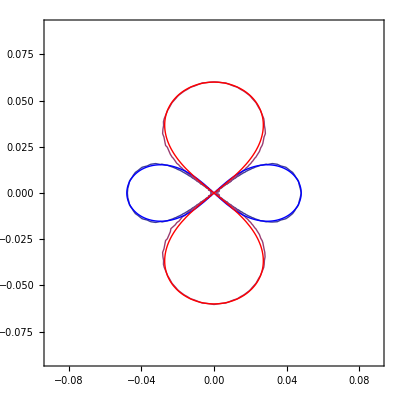

```mathematica
rg = 0.09;
r = 0.04;
cp = ContourPlot[{-(Msat r1^3 (x^2-2 z^2) μ0)/(3 (x^2+z^2)^(5/2))==(-(Freq))/γ,-(Msat r1^3 (x^2-2 z^2) μ0)/(3 (x^2+z^2)^(5/2))==(Freq)/γ}, { x,-rg,rg},{ z,-rg,rg},PerformanceGoal->"Quality"];
sc = 0.048;
pp1 =ParametricPlot[sc{Cos[t]/(1+Sin[t]^2),.9(Sin[t]Cos[t])/(1+Sin[t]^2)},{t,0,2π},PlotStyle->Blue];
pp2 =ParametricPlot[sc{1.6(Sin[t]Cos[t])/(1+Sin[t]^2),1.25 Cos[t]/(1+Sin[t]^2)},{t,0,2π},PlotStyle->Red];
Show[cp,pp1,pp2]
```

```mathematica
illumRegionb =RevolutionPlot3D[{sc Cos[t]/(1+Sin[t]^2),.9sc(Sin[t]Cos[t])/(1+Sin[t]^2)},{t,0,2π},{θ,0,π},PlotStyle->Directive[Opacity[1],Blue],RevolutionAxis->{0,0,1}];
illumRegiona =RevolutionPlot3D[{1.6sc(Sin[t]Cos[t])/(1+Sin[t]^2),1.25sc Cos[t]/(1+Sin[t]^2)},{t,0,2π},PlotStyle->Directive[Opacity[1],Red]];
```

```mathematica
comb = Graphics3D[Translate[{illumRegiona⟦1⟧,illumRegionb⟦1⟧},{rad,0,0}]];
Show[comb,PlotRange->All]
```

-Graphics3D-

```mathematica
RevolutionPlot3D
```

```mathematica
rad =0.032;
pp13 =RevolutionPlot3D[{rad+sc Cos[t]/(1+Sin[t]^2),.9sc(Sin[t]Cos[t])/(1+Sin[t]^2)} ,{t,0,2π},PlotStyle->Directive[Opacity[0.4],Blue],MeshStyle->Opacity[0.2]]; 
pp23 =RevolutionPlot3D[{rad+1.6sc(Sin[t]Cos[t])/(1+Sin[t]^2),1.25sc Cos[t]/(1+Sin[t]^2)},{t,0,2π},PlotStyle->Directive[Opacity[0.4],Red],MeshStyle->Opacity[0.2]];
```

```mathematica
Show[pp23,pp13,comb,PlotRange->All]
```

-Graphics3D-

### THis one is wrong ... we need the swept out volume, not a rotated volume

```mathematica
illumRegionbT=RevolutionPlot3D[{sc Cos[t]/(1+Sin[t]^2),.9sc(Sin[t]Cos[t])/(1+Sin[t]^2)},{t,0,2π},{θ,0,π},PlotStyle->Directive[Opacity[0.5],Blue],RevolutionAxis->{0,0,1},MeshStyle->Opacity[0.2]];
illumRegionaT =RevolutionPlot3D[{1.6sc(Sin[t]Cos[t])/(1+Sin[t]^2),1.25sc Cos[t]/(1+Sin[t]^2)},{t,0,2π},PlotStyle->Directive[Opacity[0.5],Red],MeshStyle->Opacity[0.2]];
```

```mathematica
comb = Graphics3D[Translate[{illumRegiona⟦1⟧,illumRegionb⟦1⟧},Table[rad{0,Sin[a],Cos[a]},{a,0,(1+3/4)π,π/4}]]];
Show[comb,PlotRange->All]
```

-Graphics3D-

### How close must two spheres be in order to move capsule out of magnetic field?

```mathematica
Clear[ μ0,Msat,r1,Msat,r2,m1]
m1 = {0,0,4/3 π r1^3 Msat}; (*magnetization of first dipole*)
r2 = {x,y,z};
offs = {d1x,0,d1z};
Simplify[(μ0/(4π)(3 r2/Norm[r2]((r2/Norm[r2]).m1)-m1)/Norm[r2]^3)⟦3⟧]
Simplify[(μ0/(4π)(3(r2-offs)/Norm[r2-offs](((r2-offs)/Norm[r2-offs]).m1)-m1)/Norm[r2-offs]^3)⟦3⟧]
```

-(Msat r1^3 μ0 (-3 z^2+Abs[x]^2+Abs[y]^2+Abs[z]^2))/(3 (Abs[x]^2+Abs[y]^2+Abs[z]^2)^(5/2))

-(Msat r1^3 μ0 (-3 d1z^2+6 d1z z-3 z^2+Abs[d1x-x]^2+Abs[y]^2+Abs[d1z-z]^2))/(3 (Abs[d1x-x]^2+Abs[y]^2+Abs[d1z-z]^2)^(5/2))

```mathematica
FullSimplify[-(Msat r1^3 μ0 (-3 d1z^2+6 d1z z-3 z^2+(d1x-x)^2+y^2+(d1z-z)^2))/(3 ((d1x-x)^2+y^2+(d1z-z)^2)^(5/2))]
```

-(Msat r1^3 ((d1x-x)^2+y^2-2 (d1z-z)^2) μ0)/(3 ((d1x-x)^2+y^2+(d1z-z)^2)^(5/2))

```mathematica
FullSimplify[1/3 Msat r1^3 (-(x^2+y^2-2 (d1-z)^2)/((x^2+y^2+(d1-z)^2)^(5/2))-(x^2+y^2-2 z^2)/((x^2+y^2+z^2)^(5/2))) μ0]
```

```mathematica
FullSimplify[-(Msat r1^3 μ0 (-3 z^2+x^2+y^2+z^2))/(3 (x^2+y^2+z^2)^(5/2))-(Msat r1^3 ((d1x-x)^2+y^2-2 (d1z-z)^2) μ0)/(3 ((d1x-x)^2+y^2+(d1z-z)^2)^(5/2))]
```

-(Msat r1^3 ((d1x-x)^2+y^2-2 (d1z-z)^2) μ0)/(3 ((d1x-x)^2+y^2+(d1z-z)^2)^(5/2))-(Msat r1^3 (x^2+y^2-2 z^2) μ0)/(3 (x^2+y^2+z^2)^(5/2))

```mathematica
μ0=4π 10^-7;
Msat=  1.36 10^6; (* steel in 3T*)
r1 = 0.0025; (*mm radius sphere*)
m1 = {0,4/3 π r1^3 Msat}; (*magnetization of first dipole*)
m2 =  {0,4/3 π r1^3 Msat};  (*magnetization of second dipole*)
rg =.07;
(*dz = 0.125;
dxy = 0.098;*)

γ = 42480000;(* 42480000 Hz/T  (42.48 MHz/T)*)
Freq = 3500;
BW = 2500;
dxy = ((Msat r1^3 μ0 γ)/(3 Freq))^(1/3);
dz = ((2Msat r1^3 μ0 γ)/(3 Freq))^(1/3);
mkRad = 0.0035; (*MR spot radius*)
mkHLength = 0.0085;(*MR-spot half-length*)
BField2D[{x_,y_}] := μ0/(4π)(3{x,y}/(√(x^2+y^2))(({x,y}/(√(x^2+y^2))).m1)-m1)/((√(x^2+y^2))^3);
d1xV=0.13373702001739043;
d1zV = 0.174882676967863;
Manipulate[ContourPlot[{(*-(Msat r1^3 (x^2-2 z^2) μ0)/(3 (x^2+z^2)^(5/2)),*)-(Msat r1^3 ((d1x-x)^2+y^2-2 (d1z-z)^2) μ0)/(3 ((d1x-x)^2+y^2+(d1z-z)^2)^(5/2))-(Msat r1^3 (x^2+y^2-2 z^2) μ0)/(3 (x^2+y^2+z^2)^(5/2))}/.{y->0}, { x,-2rg,.8rg},{ z,-3rg,rg},Contours->{(-(Freq-BW/2))/γ,(-(Freq))/γ,(-(Freq+BW/2))/γ,(Freq-BW/2)/γ,(Freq)/γ,(Freq+BW/2)/γ},ContourStyle->{Blue,Directive[Blue,Dashed],Blue,Red,Directive[Red,Dashed],Red},ContourShading->{None,Lighter[Blue,0.5],Lighter[Blue,0.5],None,Lighter[Red,0.8],Lighter[Red,0.8],None},
Prolog->{Orange,Opacity[0.25],(* Rectangle[{-d1xV,-d1zV},{d1xV,d1zV}]*),
Polygon[{{-d1xV,0},{0,d1zV},{d1xV,0},{0,-d1zV}}]},
Epilog->{Gray,Disk[{0,0},r1],Disk[{d1x,d1z},r1],
Yellow,EdgeForm[Black],
Rectangle[{-mkHLength,-(dz-mkRad)},{mkHLength,-(dz+mkRad)},RoundingRadius->0.005],
Rectangle[{-(dxy-mkRad),-mkHLength},{-(dxy+ mkRad),mkHLength},RoundingRadius->0.005],
Black,
Text[Style["⊥",16],{0,-dz}],
Text[Style["⊥",16],{-dxy,0}]
},FrameLabel-> {"x [m]","z [m]"},FrameTicks->{Table[Chop[.05 k],{k,-5,5}],Table[Chop[.05 k],{k,-5,5}],{},{}}
,PerformanceGoal->"Quality",MaxRecursion->4,FrameTicksStyle->Directive[16],LabelStyle->Directive[18],GridLines->Automatic,AspectRatio->Automatic],
{d1x,-0.2,0},
{d1z,-0.2,0}
]
```

### highQuality Pub version of Magnetic Range

```mathematica
Export[NotebookDirectory[]<>"../../pictures/pdf/"<>"MagneticFieldCapsuleRange1.pdf",p];
```

/Users/ab55/Desktop/git/MRIrobotics/Papers-Current/Design3AxisBiopsyRobot/code/mathematica/../../pictures/pdf/MagneticFieldCapsuleRange1.pdf

```mathematica
μ0=4π 10^-7;
Msat=  1.36 10^6; (* steel in 3T*)
r1 = 0.0025; (*mm radius sphere*)
m1 = {0,4/3 π r1^3 Msat}; (*magnetization of first dipole*)
m2 =  {0,4/3 π r1^3 Msat};  (*magnetization of second dipole*)
rg =.07;
(*dz = 0.125;
dxy = 0.098;*)

γ = 42480000;(* 42480000 Hz/T  (42.48 MHz/T)*)
Freq = 3500;
BW = 2500;
dxy = ((Msat r1^3 μ0 γ)/(3 Freq))^(1/3);
dz = ((2Msat r1^3 μ0 γ)/(3 Freq))^(1/3);
mkRad = 0.0035; (*MR spot radius*)
mkHLength = 0.0085;(*MR-spot half-length*)
BField2D[{x_,y_}] := μ0/(4π)(3{x,y}/(√(x^2+y^2))(({x,y}/(√(x^2+y^2))).m1)-m1)/((√(x^2+y^2))^3);
d1xV=0.13373702001739043;
d1zV = 0.174882676967863;
d1xs = {-14/100,-d1xV,-10/100,-8/100,0,0,0};
d1zs={0,0,0,-8/100,-18/100,-d1zV ,-14/100};
xMinR = {-2rg,-2rg,-2rg,-2rg,-rg,-rg,-rg};
zMinR = {-rg,-rg,-rg,-3rg,-3rg,-3rg,-3rg};
Table[d1x = d1xs⟦k⟧;d1z = d1zs⟦k⟧;
MagneticFieldCapsuleRange=contourDensityPlot[1/3 Msat r1^3 (-((d1x-x)^2-2 (d1z-z)^2)/(((d1x-x)^2+(d1z-z)^2)^(5/2))+(-x^2+2 z^2)/((x^2+z^2)^(5/2))) μ0, { x,xMinR⟦k⟧,.8rg},{ z,zMinR⟦k⟧,rg},
Contours->{(-(Freq-BW/2))/γ,(-(Freq))/γ,(-(Freq+BW/2))/γ,(Freq-BW/2)/γ,(Freq)/γ,(Freq+BW/2)/γ},Frame->True,

ContourStyle->{Blue,Directive[Blue,Dashed],Blue,Red,Directive[Red,Dashed],Red},ContourShading->{None,Lighter[Blue,0.5],Lighter[Blue,0.5],None,Lighter[Red,0.8],Lighter[Red,0.8],None},
Prolog->{Orange,Opacity[0.45],(* Rectangle[{-d1xV,-d1zV},{d1xV,d1zV}]*),
Polygon[{{-d1xV,0},{0,d1zV},{d1xV,0},{0,-d1zV}}]},
Epilog->{Gray,Disk[{0,0},r1],Disk[{d1x,d1z},r1],
Yellow,EdgeForm[Black],
Rectangle[{-mkHLength,-(dz-mkRad)},{mkHLength,-(dz+mkRad)},RoundingRadius->0.005],
Rectangle[{-(dxy-mkRad),-mkHLength},{-(dxy+ mkRad),mkHLength},RoundingRadius->0.005],
Black,
Text[Style["⊥",16],{0,-dz}],
Text[Style["⊥",16],{-dxy,0}]
}(*,FrameLabel-> {"x [m]","z [m]"}*),PlotRange->{{ -2rg,.8rg},{ -3rg,rg}},FrameTicks->{Table[Chop[.1 k],{k,-5,5}],Table[Chop[.1 k],{k,-5,5}],{},{}}
,LabelStyle->Directive[18],GridLines->Automatic,AspectRatio->Automatic,(*WorkingPrecision->20,PlotPoints->150,*)
PerformanceGoal->"Quality",FrameTicksStyle->Directive[24],LabelStyle->Directive[24],ImageSize-> Medium,"ShadingOpacity"->0.7,MaxRecursion->4];
Export[NotebookDirectory[]<>"../../pictures/pdf/"<>"MagneticFieldCapsuleRange"<>ToString[k]<>".pdf",MagneticFieldCapsuleRange];
MagneticFieldCapsuleRange,
{k,Length[d1xs]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Find the place where the the capsule is no longer illuminated by the marker.

```mathematica
NSolve[1/3 Msat r1^3 (-1/(((d1x-x)^2)^(3/2))-1/((x^2)^(3/2))) μ0==(-(Freq))/γ/.{x->((Msat r1^3 μ0 γ)/(3 Freq))^(1/3)+mkRad},d1x]
```

{{d1x→0.133737},{d1x→0.0924321+0.0715422 ⅈ},{d1x→0.0924321-0.0715422 ⅈ},{d1x→0.00982223+0.0715422 ⅈ},{d1x→0.00982223-0.0715422 ⅈ},{d1x→-0.0314827}}

```mathematica
NSolve[1/3 Msat r1^3 (2/(((d1z-z)^2)^(3/2))+2/((z^2)^(3/2))) μ0==Freq/γ/.{z->((2Msat r1^3 μ0 γ)/(3 Freq))^(1/3)+mkRad},d1z]
```

{{d1z→0.174883},{d1z→0.119195+0.0964546 ⅈ},{d1z→0.119195-0.0964546 ⅈ},{d1z→0.00781835+0.0964546 ⅈ},{d1z→0.00781835-0.0964546 ⅈ},{d1z→-0.0478698}}

```mathematica
Clear[r1, Msat, μ0,Freq,γ]
FullSimplify[-(Msat r1^3 (x^2) μ0)/(3 (x^2)^(5/2))==-Freq/γ](*pos freq*)
FullSimplify[-(Msat r1^3 (-2 z^2) μ0)/(3 (z^2)^(5/2))==Freq/γ](*neg freq*)
```

```mathematica
Freq/γ==(Msat r1^3 μ0)/(3 (x^3))
dxy = ((Msat r1^3 μ0 γ)/(3 Freq))^(1/3)
dz = ((Msat r1^3 μ0 γ)/(3 Freq))^(1/3)
```

{{x→-((-1/3)^(1/3) Msat^(1/3) r1 γ^(1/3) μ0^(1/3))/Freq^(1/3)},{x→(Msat^(1/3) r1 γ^(1/3) μ0^(1/3))/(3^(1/3) Freq^(1/3))},{x→((-1)^(2/3) Msat^(1/3) r1 γ^(1/3) μ0^(1/3))/(3^(1/3) Freq^(1/3))}}

(2 Msat r1^3 μ0)/(3 z^3)==Freq/γ

```mathematica
Clear[x,z,μ0,Msat,r1,m1]
m1 = {0,4/3 π r1^3 Msat};
FullSimplify[ μ0/(4π)(3{x,z}/(√(x^2+z^2))(({x,z}/(√(x^2+z^2))).m1)-m1)/((√(x^2+z^2))^3)]
```

{(Msat r1^3 x z μ0)/((x^2+z^2)^(5/2)),-(Msat r1^3 (x^2-2 z^2) μ0)/(3 (x^2+z^2)^(5/2))}

```mathematica
Clear[x,z,μ0,Msat,r1,m1]
{-(Msat r1^3 ((d1x-x)^2+y^2-2 (d1z-z)^2) μ0)/(3 ((d1x-x)^2+y^2+(d1z-z)^2)^(5/2))-(Msat r1^3 (x^2+y^2-2 z^2) μ0)/(3 (x^2+y^2+z^2)^(5/2))}/.{y->0}
```

```mathematica
(*these are the magnetic fields in the x and z directions.
FullSimplify[{-(Msat r1^3 ((d1x-x)^2-2 (d1z-z)^2) μ0)/(3 ((d1x-x)^2+(d1z-z)^2)^(5/2))-(Msat r1^3 (x^2-2 z^2) μ0)/(3 (x^2+z^2)^(5/2))}]
We want to find the area where the magnetic field == (+/-(Freq))/γ within mkRad = 0.0035; , the MR spot radius.

dxy = ((Msat r1^3 μ0 γ)/(3 Freq))^(1/3)
dz = ((Msat r1^3 μ0 γ)/(3 Freq))^(1/3)

*)
```

```mathematica
Clear[mkRad,Msat, r1,μ0 ,Freq,γ]
{1/3 Msat r1^3 (-((d1x-x)^2-2 (d1z-z)^2)/(((d1x-x)^2+(d1z-z)^2)^(5/2))+(-x^2+2 z^2)/((x^2+z^2)^(5/2))) μ0}/.{d1x->0,x->0}
{1/3 Msat r1^3 (-((d1x-x)^2-2 (d1z-z)^2)/(((d1x-x)^2+(d1z-z)^2)^(5/2))+(-x^2+2 z^2)/((x^2+z^2)^(5/2))) μ0}/.{d1z->0,z->0}
```

### Plot of forces on Dipole

```mathematica
contourDensityPlot[f_,rx_,ry_,opts:OptionsPattern[]]:=(* //Created by Jens U.Nöckel for Mathematica 8,revised 12/2011, http://pages.uoregon.edu/noeckel/computernotes/Mathematica/contourDensityPlot.html*)Module[{img,cont,pL,p,plotRangeRule,densityOptions,contourOptions,frameOptions,rangeCoords},densityOptions=Join[FilterRules[{opts},FilterRules[Options[ContourPlot],Except[{ImageSize,Prolog,Epilog,FrameTicks,PlotLabel,ImagePadding,GridLines,Mesh,AspectRatio,ContourStyle,PlotRangePadding,Frame,Axes}]]],{PlotRangePadding->None,ImagePadding->None,Frame->None,Axes->None}];
pL=ContourPlot[f,rx,ry,Evaluate@Apply[Sequence,densityOptions],ContourStyle->None];
p=First@Cases[{pL},Graphics[__],∞];
plotRangeRule=FilterRules[AbsoluteOptions[p],PlotRange];
contourOptions=Join[FilterRules[{opts},FilterRules[Options[ContourPlot],Except[{Prolog,Epilog,FrameTicks,Background,ContourShading,Frame,Axes}]]],{Frame->None,Axes->None,(*ContourShading->Reverse[{Lighter[Blue,0],Lighter[Blue,0.5],Lighter[Blue,0.8],Lighter[Red,0.8],Lighter[Red,0.5],Lighter[Red,0]}] *)ContourShading->False}];
(* //The density plot img and contour plot cont are created here:*)
img=Rasterize[p,"Image"];
cont=If[MemberQ[{0,None},(Contours/.FilterRules[{opts},Contours])],{},ContourPlot[f,rx,ry,Evaluate@Apply[Sequence,contourOptions]]];
(* //Before showing the plots,set the PlotRange for the frame which will be drawn separately:*)frameOptions=Join[FilterRules[{opts},FilterRules[Options[Graphics],Except[{PlotRangeClipping,PlotRange}]]],{plotRangeRule,Frame->True,PlotRangeClipping->True}];
rangeCoords=Transpose[PlotRange/.plotRangeRule];
(* //To align the image img with the contour plot,enclose img in a//bounding box rectangle of the same dimensions as cont,
//and then combine with cont using Show:*)If[Head[pL]===Legended,Legended[#,pL[[2]]],#]&@Show[Graphics[{Inset[Show[SetAlphaChannel[img,"ShadingOpacity"/.{opts}/.{"ShadingOpacity"->1}],AspectRatio->Full],rangeCoords[[1]],{0,0},rangeCoords[[2]]-rangeCoords[[1]]]},PlotRangePadding->None],cont,Evaluate@Apply[Sequence,frameOptions]]]
```

```mathematica
plotMagnet[rad_]:= {Lighter[Gray],Disk[{0,0},rad],Darker[Red],Disk[{0,0},rad,{0,Pi}],Black,Circle[{0,0},rad]};
r1=0.0025;
pr =0.07; (*4.404597813943813 r1;*)
μ0=4π 10^-7;
Msat=  1.36 10^6;
maxGrad = 0.04;
mg = 100000 maxGrad 4/3 π r1^3 Msat;
dxy = ((Msat r1^3 μ0 γ)/(3 Freq))^(1/3);
dz = ((2Msat r1^3 μ0 γ)/(3 Freq))^(1/3);
mkRad = 0.0035; (*MR spot radius*)
mkHLength = 0.0085;(*MR-spot half-length*)

γ = 42480000;(* 42480000 Hz/T  (42.48 MHz/T)*)
Freq = 3500;
minFrac = 1/10;
rCp = contourDensityPlot[Min[{mg ,Max[{-mg ,((4 Msat^2 π r1^6 x (x^2-4 y^2) μ0)/(3 (x^2+y^2)^(7/2))x/√(x^2+y^2)+(4 Msat^2 π r1^6 (3 x^2 y-2 y^3) μ0)/(3 (x^2+y^2)^(7/2))y/√(x^2+y^2))}]}],{x,-pr,pr},{y,-pr,pr},
Contours->Table[4/3 π r1^3 Msat grad,{grad,{-maxGrad,-maxGrad minFrac,0,maxGrad minFrac,maxGrad}}],Frame->True,FrameLabel->{"y [m]","z [m]"(*None*)},ContourShading->Reverse[{Lighter[Blue,0],Lighter[Blue,0.5],Lighter[Blue,0.8],Lighter[Red,0.8],Lighter[Red,0.5],Lighter[Red,0]}],(*RegionFunction->Function[{x,y,vx,vy,n},x^2+y^2>r1^2],*)

Epilog->{Gray,(*Disk[{0,0},r1],*)
plotMagnet[r1],Opacity[0.5],
Yellow,EdgeForm[Black],
Rectangle[{-mkHLength,-(dz-mkRad)},{mkHLength,-(dz+mkRad)},RoundingRadius->0.005],
Rectangle[{-(dxy-mkRad),-mkHLength},{-(dxy+ mkRad),mkHLength},RoundingRadius->0.005],
Black,
Text[Style["⊥",16],{0,-dz}],
Text[Style["⊥",16],{-dxy,0}]
},PlotRange->All,(*Axes->True,*)
FrameTicks->{{-0.05,0,0.05},{-0.05,0,0.05},{},{}},PerformanceGoal->"Quality"FrameTicksStyle->Directive[16],LabelStyle->Directive[18],ImageSize-> Medium,"ShadingOpacity"->0.7,GridLines->Automatic]
```

-Graphics-

```mathematica
pr = 0.01;
r1=0.001;
Plot3D[(4 Msat^2 π r1^6 x (x^2-4 y^2) μ0)/(3 (x^2+y^2)^(7/2))x/√(x^2+y^2)+(4 Msat^2 π r1^6 (3 x^2 y-2 y^3) μ0)/(3 (x^2+y^2)^(7/2))y/√(x^2+y^2)/.{μ0->4π 10^-7,Msat->  1.36 10^6},{x,-pr,pr},{y,-pr,pr},RegionFunction->Function[{x,y,vx,vy,n},x^2+y^2>r1^2]]
```

-Graphics3D-

## How far should Magnets be separated so that gradient forces dominant?

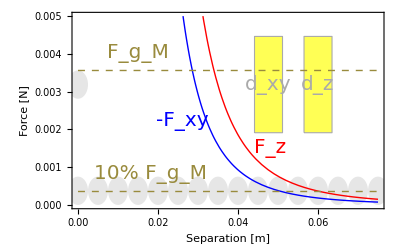

```mathematica
μ0=4π 10^-7;
Msat=  1.36 10^6; (* steel in 3T*)
r1 = 0.0025; (*mm radius sphere*)
fz = 20;  (*  -(8 Msat^2 π r1^3 r2^3 μ0)/(3 y^4)   *)
Fxy[x_,r1_,r2_]:=(4 Msat^2 π r1^3 r2^3 μ0)/(3 x^4);
Fz[z_,r1_,r2_]:= -(8 Msat^2 π r1^3 r2^3 μ0)/(3 z^4);
maxGrad = 0.04;(* Teslas *)
mg = maxGrad 4/3 π r1^3 Msat;

mkRad = 0.0035; (*MR spot radius*)
mkHLength = 0.0085;(*MR-spot half-length*)
xrg = 30;
zrg = 0.005;
vs = .15;
γ = 42480000;(* 42480000 Hz/T  (42.48 MHz/T)*)
Freq = 3500;
BW = 2500;
dxy = ((Msat r1^3 μ0 γ)/(3 Freq))^(1/3);
dz = ((2Msat r1^3 μ0 γ)/(3 Freq))^(1/3);
h = 8.5;
Plot[{Fxy[x,r1,r1],-Fz[x,r1,r1],mg,mg/10},{x,0,xrg r1},

PlotRange->{{0,xrg r1},{0,zrg}},
PlotStyle->{Blue,Red,Directive[Dashed,ColorData[1,3]],Directive[Dashed,ColorData[1,3]]},Prolog->{Thick,Lighter[LightGray],Table[Disk[{k 2 r1 ,vs r1},{r1,vs r1}],{k,0,20}],
Disk[{0 ,vs h r1},{r1,vs r1}],
Lighter[Yellow],EdgeForm[Lighter[Gray]],(*Disk[{dz,vs 6 r1},{mkRad,vs mkHLength}],*)
Rectangle[{dz-mkRad,vs( h r1-mkHLength)},{dz+mkRad,vs( h r1+mkHLength)},RoundingRadius->{0.003,vs 0.003}],
Rectangle[{dxy-mkRad,vs( h r1-mkHLength)},{dxy+mkRad,vs( h r1+mkHLength)},RoundingRadius->{0.003,vs 0.003}],
Lighter[Gray],Text[Style[" d_xy",fz],{dxy,vs h r1}],
Text[Style["d_z",fz],{dz,vs h r1}],
Blue,Text[Style["-F_xy",fz],{0.026,0.0022}],
Red,Text[Style["F_z",fz],{0.048,0.0015}],
ColorData[1,3],Text[Style["F_g_M",fz],{0.015,0.004}],
Text[Style["10% F_g_M",fz],{0.018,0.0008}]
(*Yellow,EdgeForm[Black],
Rectangle[{-mkRad,-vs mkHLength},{mkRad,vs mkHLength},RoundingRadius->50]*)
},
Frame->{True,True,False,False},
AxesOrigin->{0,0},FrameLabel-> {"Separation [m]","Force [N]"},(*FrameTicks->{{-0.04,0,0.04},{-0.04,0,0.04},{},{}},*)PerformanceGoal->"Quality",FrameTicksStyle->Directive[16],LabelStyle->Directive[18]]
```

```mathematica
Sqrt[.3/300]
```

0.0316228

```mathematica
7.84/300
```

0.0261333

```mathematica
0.32/7.48
```

0.0427807